```mathematica
(* What value of m makes this circle to have radius zero? *)
sol=Solve[3 x^2+3 y^2+60x+180 y+75 m ==0, y]
```

{{y→-30-√(900-25 m-20 x-x^2)},{y→-30+√(900-25 m-20 x-x^2)}}

```mathematica
y[x_]:= -30+√(900-25 m-20 x-x^2)
ym[x_]:= -30-√(900-25 m-20 x-x^2)
```

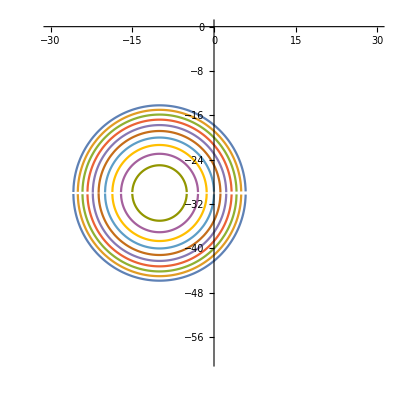

```mathematica
Plot[Table[{y[x], ym[x]}, {m, 30, 40}], {x, -100, 100}, {Evaluated->True, PlotRange->{{-30,30},{-60,0}}, AspectRatio->1}]
```

```mathematica
Maximize[y[x], x]
```

{Piecewise[{{5 (-6+√(40-m)), m≤40}, {-∞, True}}],{x→Piecewise[{{-10, m≤40}, {Indeterminate, True}}]}}

```mathematica
(* So, m = 40 does it. *)
Solve[y[-10]==-30, m]
```

{{m→40}}

```mathematica
(* Again: *)
```

```mathematica
eq = 3 x^2+3 y^2+60x+180 y ==-75m
```

60 x+3 x^2+180 y+3 y^2==-75 m

```mathematica
lhs=eq[[1]]
```

60 x+3 x^2+180 y+3 y^2

```mathematica
(* Divide all by three *)
```

```mathematica
lhs/3==-75m/3//Expand
```

20 x+x^2+60 y+y^2==-25 m

```mathematica
(* Complete the square: *)
```

```mathematica
(x+10)^2+(y+30)^2==-25m+1000//Expand
```

1000+20 x+x^2+60 y+y^2==1000-25 m

```mathematica
Solve[1000-25 m==0, m]
```

{{m→40}}